```mathematica
Pulse[t_,ts_]:= Piecewise[{{-t Exp[-t/ts], t>0},{0, t≤0}}]
```

```mathematica
Integrate[t Exp[-t],{t,0,∞}]
```

1

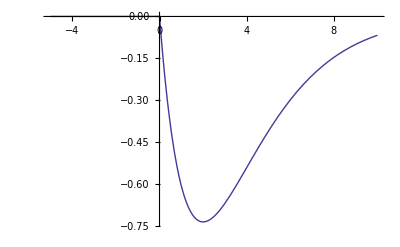

```mathematica
Plot[Pulse[t,2],{t,-5,10}]
```

```mathematica
Charge[T_,ts_,gate_]:=Integrate[-Pulse[t,ts],{t,T,T+gate},Assumptions->{T,gate}∈ Reals]
```

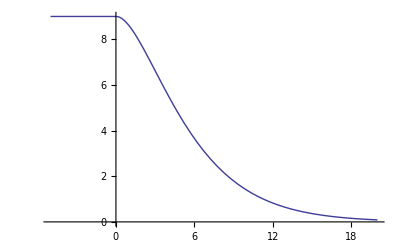

```mathematica
Plot[Charge[T,3],{T,-5, 20}]
```

```mathematica
Charge[T,1,200]
```

Piecewise[{{ⅇ^(-200-T) (-201+ⅇ^(200+T)-T), -200<T≤0}, {ⅇ^(-200-T) (-201+ⅇ^200-T+ⅇ^200 T), T>0}, {0, True}}]

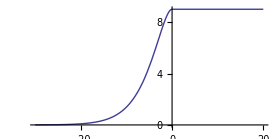

```mathematica
Plot[Charge[-T,3],{T,-30, 20},AspectRatio->0.5,PlotRange->{{-30,20},{0, All}}]
```

```mathematica
Data={
{-248,2698},
{-244,2961},
{-240,3283},
{-254,2363},
{-262,2100},
{-276,1850},
{-289,1695},
{-304,1563},
{-320,1468}};
```

```mathematica
K=FindFit[Data, a Exp[(t-α)/t1]+b Exp[(t-β)/t2],{a,b,t1,t2,α,β},t]
```

{a→1.,b→1.,t1→1.,t2→1.,α→1.,β→1.}

```mathematica
f=Interpolation[Data]
```

InterpolatingFunction[{{-320,-240}},<>]

```mathematica
Manipulate[
Show[{
Plot[{ a Exp[(t-α)/t1]+b Exp[(t-β)/t2],f[t]},{t,-320,-230}], 
ListPlot[Data]
}],
{{a,10800},0,20000},
{{α,-205},-400, -100},
{{t1,17.75},2, 25},
{{b,1740},0,4000},
{{β,-250},-400, -100},
{{t2,400},2, 500}]
```

```mathematica
Data={
{-238,3431},
{-248,2698},
{-244,2961},
{-240,3283},
{-254,2363},
{-262,2100}};
```

```mathematica
Manipulate[
Show[{
Plot[{  a (t-t1)^α,f[t]},{t,-270,-210}], 
ListPlot[Data]
}],
{{a,200},0,8000},
{{t1,-250},-270, -210},
{{α,1},1, 5}]
```